## LECs declaration

LCDa = Johannes parameters
LCDb = E2: -1      MeV    E3: -3       MeV  from PJM paper
LCDc = E2: -2.22 MeV    E3: -8.48  MeV Nuclear case
LCDd = Unitary               E3: -10 MeV

```mathematica
(* Johannes fitting parameters a=12 c.a. *)
LCDo={{25, 0.40386299,-2929.4763,89436.1852}};
```

```mathematica
(* Johannes fitting parameters a=12 c.a. *)
LCDa={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

```mathematica
(* E2=1 E3=3 *)
LCDb={{0.05,1,-1.55166500,0.1329927285},{0.1,1,-2.24166300,0.3701120098},{0.16,1,-3.44040000,1.138524898},{0.2,1,-4.04022700,1.249910638},{0.3,1,-6.39651000,2.799024416},{0.35,1,-7.80830000,3.936630847},{0.4,1,-9.31007578,5.177438097},{0.45,1,-10.97613646,6.72964684},{0.5,1,-12.78163000,8.552092744},{0.55,1,-14.72581116,10.66423485},{0.6,1,-16.80907468,13.08996044},{0.65,1,-19.03174482,15.85408},{0.7,1,-21.39405000,18.9824788},{0.75,1,-23.89403709,22.49131818},{0.8,1,-26.53580000,26.42858035},{0.9,1,-32.23375000,35.64420878},{0.95,1,-35.29122000,40.98921369},{1,1,-38.48853000,46.87432648},{1.05,1,-41.82441000,53.32423158},{1.1,1,-45.29949000,60.37950916},{1.2,1,-52.66596000,76.44622944},{1.5,1,-78.11106000,143.6179272},{2,1,-131.64598000,346.2149284},{3,1,-280.45691000,1468.17912},{4,1,-484.92093000,5254.800421},{6,1,-1060.79670000,61617.93639},{10,1,-2880.38650000,12838191.7}};
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 *)
LCDc={{0.1,1,	0	,0},{0.16,1,-5.23609711,-0.2508527567},{0.2,1,-6.21155090,-0.01411577035},{0.3,1,-9.04089890,0.9058334635},{0.35,1,-10.66481819,1.562725218},{0.4,1,-12.42824554,2.36543082},{0.45,1,-14.33104515,3.3244409},{0.5,1,-16.37322998,4.450396189},{0.55,1,-18.55475197,5.753778748},{0.6,1,-20.87557983,7.245120228},{0.65,1,-23.33569527,8.935015304},{0.7,1,-25.93508911,10.83416803},{0.75,1,-28.67371368,12.95315533},{0.8,1,-31.55156555,15.30282946},{0.85,1,-34.56868362,17.89442822},{0.9,1,-37.72501221,20.7388847},{0.95,1,-41.02048416,23.84721094},{1,1,-44.45520020,27.23128363},{1.05,1,-48.02915573,30.90286676},{1.1,1,-51.74223328,34.87341855},{1.2,1,-59.58599854,43.76101396},{1.5,1,-86.45745087,78.9169705},{2,1,-142.37614441,172.7038298},{3,1,-295.95935059,559.0134636},{4,1,-505.20166016,1397.569451},{6,1,-1090.66113281,6311.303676},{10,1,-2929.47631836,89436.18522}};
```

```mathematica
(*Unitary E3=10*)
LCDd={{3,1,-250.617,101.932316},{4,1,-445.542,327.529341},{5,1,-696.159,726.927273},{6,1,-1002.47,1363.978137},{7,1,-1364.47,2321.631926},{8,1,-1782.17,3709.828715}};
```

## Solvers

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif])+(L(L+1))/i^2,{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

If[p==0,

bcol=Table[Which[i==nnGrid,-hDif,1==1,0],{i,1,nnGrid}];
Dmat⟦nnGrid⟧⟦nnGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;
ddmat=Dmat;
wwmat=Wmat;
kkmat=Kmat;
aamat=Amat;
bbvec=bcol;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=RRmax-usol⟦-1⟧;
,

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p Rmax];

usol=LinearSolve[Amat,bcol];
ddmat=Dmat;
wwmat=Wmat;
kkmat=Kmat;
aamat=Amat;
bbvec=bcol;

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=p^(2L+1) ((usol⟦-1⟧-Sin[p RRmax])/Cos[p RRmax])^-1;
];

{Tere,wf}
]
```

```mathematica
SolveSecularNL1[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,tanDelta,fit,nn,δ,L,r,mod,usol,lam,lec},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif]-(L(L+1))/(i hDif)^2),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;

If[p==0,
(* ------------------------- zer0 momentum ------------------------- *)

If[L==0,
bcol⟦-1⟧=- hDif;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1
,
bcol[[-1]]=1-1./nnGrid;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+hDif^2 nnGrid;
];

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];

If[L==0,
tanDelta=RRmax-usol⟦-1⟧;
,
tanDelta=RRmax^3/3-usol⟦-1⟧ RRmax;
tanDelta=RRmax-usol⟦-1⟧;
];
,
(* ------------------------- non-zer0 momentum --------------------- *)

(*bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);*)
bcol⟦-1⟧=- beta[RRmax,p,L,hDif];
(*Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p RRmax];*)
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[RRmax,p,L,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
tanDelta= (RiccatiBesselJ[p RRmax,L]/RiccatiBesselN[p RRmax,L])-(usol⟦-1⟧/RiccatiBesselN[p RRmax,L]);
];

{tanDelta,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
(* 1/2 is to have μ instead of m*)
f=Replace[w,NDSolve[{w'[r]+w[r]^2- mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Solve

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
(*m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
Λl={2.,4.,6.,8.,10.};*)
```

```mathematica
(*
LCDa=Johannes parameters
LCDb=E2:-1 MeV E3:-3 MeV from PJM paper
LCDc=E2:-2.22 MeV E3:-8.48 MeV Nuclear case
LCDd=Unitary E3:-10 MeV
*)

LCD = LCDc;
m=938.92;
μ=m/2;
```

```mathematica
(* Options: *)
Fit2b = False;  (* Do you want to fit the two body lec?*)
aleph = 1/12;  (* In case to which aleph*)

CalculateFF=False;          (*Calcualte Fermion-Fermion scattering*)
CalculateDD =False;         (*Calcualte Dimer-Dimer scattering*)
CalculateDDstar=False; (*Calculate ab-ac scattering*)
Calculate4H =True;         (*Calculate a-abc scattering*)
```

{λ = ,0.1,   C0 = ,0,   D0 = ,0}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

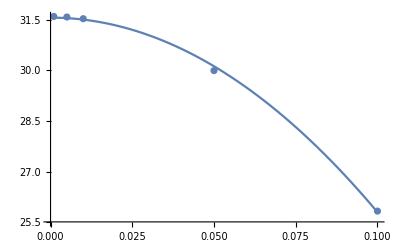

t-f: (finite momentum)   a_(d^*) = -0.0316854     r_(d^*) = -1151.54

>> The pole is at: {{p→-0.234124-0.0000476004 ⅈ},{p→0.+575.771 ⅈ},{p→0.234124-0.0000476004 ⅈ}}

--

{λ = ,0.16,   C0 = ,-5.2361,   D0 = ,-0.250853}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

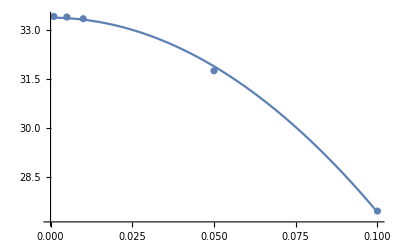

t-f: (finite momentum)   a_(d^*) = -0.0299558     r_(d^*) = -1189.56

>> The pole is at: {{p→-0.236909-0.0000471818 ⅈ},{p→0.+594.781 ⅈ},{p→0.236909-0.0000471818 ⅈ}}

--

{λ = ,0.2,   C0 = ,-6.21155,   D0 = ,-0.0141158}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

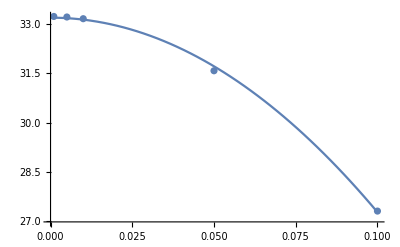

t-f: (finite momentum)   a_(d^*) = -0.0301218     r_(d^*) = -1185.65

>> The pole is at: {{p→-0.236645-0.0000472322 ⅈ},{p→0.+592.824 ⅈ},{p→0.236645-0.0000472322 ⅈ}}

--

{λ = ,0.3,   C0 = ,-9.0409,   D0 = ,0.905833}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

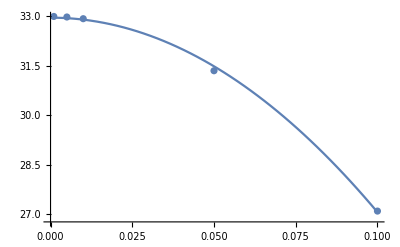

t-f: (finite momentum)   a_(d^*) = -0.0303384     r_(d^*) = -1180.61

>> The pole is at: {{p→-0.236301-0.0000472961 ⅈ},{p→0.+590.305 ⅈ},{p→0.236301-0.0000472961 ⅈ}}

--

{λ = ,0.35,   C0 = ,-10.6648,   D0 = ,1.56273}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

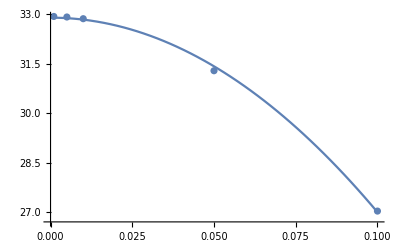

t-f: (finite momentum)   a_(d^*) = -0.0303943     r_(d^*) = -1179.32

>> The pole is at: {{p→-0.236213-0.0000473123 ⅈ},{p→0.+589.66 ⅈ},{p→0.236213-0.0000473123 ⅈ}}

--

{λ = ,0.4,   C0 = ,-12.4282,   D0 = ,2.36543}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

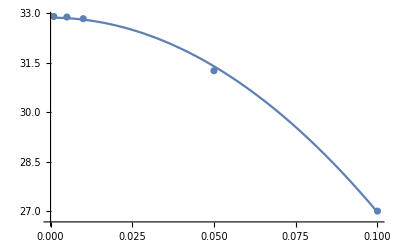

t-f: (finite momentum)   a_(d^*) = -0.0304321     r_(d^*) = -1178.45

>> The pole is at: {{p→-0.236153-0.0000473232 ⅈ},{p→0.+589.226 ⅈ},{p→0.236153-0.0000473232 ⅈ}}

--

{λ = ,0.45,   C0 = ,-14.331,   D0 = ,3.32444}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

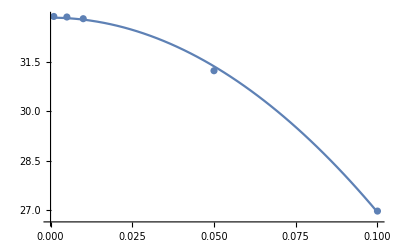

t-f: (finite momentum)   a_(d^*) = -0.0304579     r_(d^*) = -1177.86

>> The pole is at: {{p→-0.236112-0.0000473306 ⅈ},{p→0.+588.93 ⅈ},{p→0.236112-0.0000473306 ⅈ}}

--

{λ = ,0.5,   C0 = ,-16.3732,   D0 = ,4.4504}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

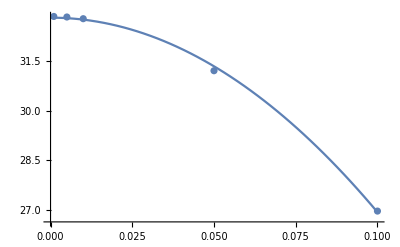

t-f: (finite momentum)   a_(d^*) = -0.0304752     r_(d^*) = -1177.46

>> The pole is at: {{p→-0.236085-0.0000473357 ⅈ},{p→0.+588.731 ⅈ},{p→0.236085-0.0000473357 ⅈ}}

--

{λ = ,0.55,   C0 = ,-18.5548,   D0 = ,5.75378}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

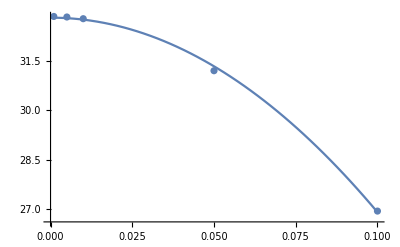

t-f: (finite momentum)   a_(d^*) = -0.0304865     r_(d^*) = -1177.2

>> The pole is at: {{p→-0.236067-0.000047339 ⅈ},{p→0.+588.601 ⅈ},{p→0.236067-0.000047339 ⅈ}}

--

{λ = ,0.6,   C0 = ,-20.8756,   D0 = ,7.24512}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

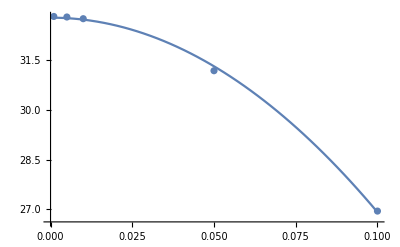

t-f: (finite momentum)   a_(d^*) = -0.0304933     r_(d^*) = -1177.05

>> The pole is at: {{p→-0.236057-0.0000473411 ⅈ},{p→0.+588.523 ⅈ},{p→0.236057-0.0000473411 ⅈ}}

--

{λ = ,0.65,   C0 = ,-23.3357,   D0 = ,8.93502}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

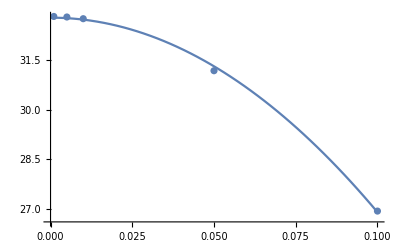

t-f: (finite momentum)   a_(d^*) = -0.0304967     r_(d^*) = -1176.97

>> The pole is at: {{p→-0.236051-0.0000473423 ⅈ},{p→0.+588.483 ⅈ},{p→0.236051-0.0000473423 ⅈ}}

--

{λ = ,0.7,   C0 = ,-25.9351,   D0 = ,10.8342}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

-Graphics-

t-f: (finite momentum)   a_(d^*) = -0.0304975     r_(d^*) = -1176.94

>> The pole is at: {{p→-0.23605-0.0000473428 ⅈ},{p→0.+588.472 ⅈ},{p→0.23605-0.0000473428 ⅈ}}

--

{λ = ,0.75,   C0 = ,-28.6737,   D0 = ,12.9532}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

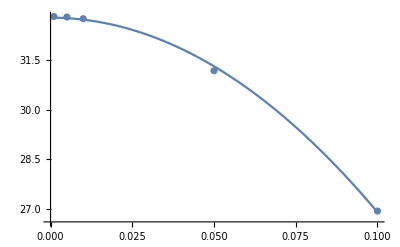

t-f: (finite momentum)   a_(d^*) = -0.0304963     r_(d^*) = -1176.97

>> The pole is at: {{p→-0.236053-0.0000473426 ⅈ},{p→0.+588.484 ⅈ},{p→0.236053-0.0000473426 ⅈ}}

--

{λ = ,0.8,   C0 = ,-31.5516,   D0 = ,15.3028}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

-Graphics-

t-f: (finite momentum)   a_(d^*) = -0.0304935     r_(d^*) = -1177.03

>> The pole is at: {{p→-0.236057-0.0000473421 ⅈ},{p→0.+588.515 ⅈ},{p→0.236057-0.0000473421 ⅈ}}

--

{λ = ,0.85,   C0 = ,-34.5687,   D0 = ,17.8944}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

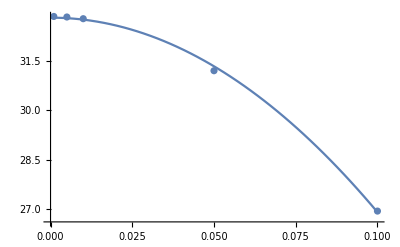

t-f: (finite momentum)   a_(d^*) = -0.0304895     r_(d^*) = -1177.12

>> The pole is at: {{p→-0.236064-0.0000473411 ⅈ},{p→0.+588.56 ⅈ},{p→0.236064-0.0000473411 ⅈ}}

--

{λ = ,0.9,   C0 = ,-37.725,   D0 = ,20.7389}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

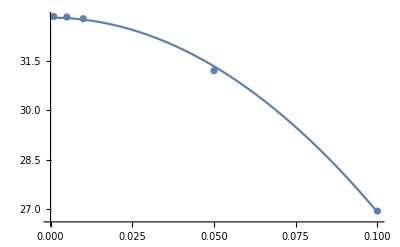

t-f: (finite momentum)   a_(d^*) = -0.0304844     r_(d^*) = -1177.23

>> The pole is at: {{p→-0.236072-0.0000473399 ⅈ},{p→0.+588.617 ⅈ},{p→0.236072-0.0000473399 ⅈ}}

--

{λ = ,0.95,   C0 = ,-41.0205,   D0 = ,23.8472}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

-Graphics-

t-f: (finite momentum)   a_(d^*) = -0.0304785     r_(d^*) = -1177.37

>> The pole is at: {{p→-0.236082-0.0000473385 ⅈ},{p→0.+588.683 ⅈ},{p→0.236082-0.0000473385 ⅈ}}

--

{λ = ,1,   C0 = ,-44.4552,   D0 = ,27.2313}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

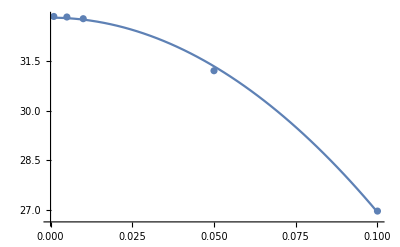

t-f: (finite momentum)   a_(d^*) = -0.0304719     r_(d^*) = -1177.51

>> The pole is at: {{p→-0.236093-0.0000473368 ⅈ},{p→0.+588.757 ⅈ},{p→0.236093-0.0000473368 ⅈ}}

--

{λ = ,1.05,   C0 = ,-48.0292,   D0 = ,30.9029}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

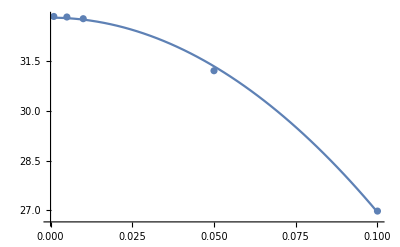

t-f: (finite momentum)   a_(d^*) = -0.0304647     r_(d^*) = -1177.67

>> The pole is at: {{p→-0.236104-0.000047335 ⅈ},{p→0.+588.837 ⅈ},{p→0.236104-0.000047335 ⅈ}}

--

{λ = ,1.1,   C0 = ,-51.7422,   D0 = ,34.8734}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

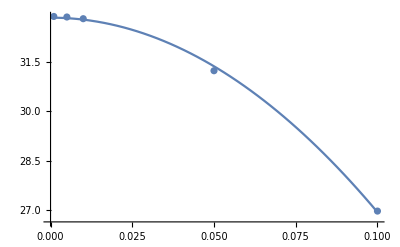

t-f: (finite momentum)   a_(d^*) = -0.0304571     r_(d^*) = -1177.85

>> The pole is at: {{p→-0.236117-0.000047333 ⅈ},{p→0.+588.923 ⅈ},{p→0.236117-0.000047333 ⅈ}}

--

{λ = ,1.2,   C0 = ,-59.586,   D0 = ,43.761}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

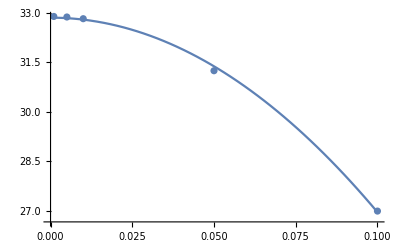

t-f: (finite momentum)   a_(d^*) = -0.0304409     r_(d^*) = -1178.21

>> The pole is at: {{p→-0.236143-0.0000473288 ⅈ},{p→0.+589.106 ⅈ},{p→0.236143-0.0000473288 ⅈ}}

--

{λ = ,1.5,   C0 = ,-86.4575,   D0 = ,78.917}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

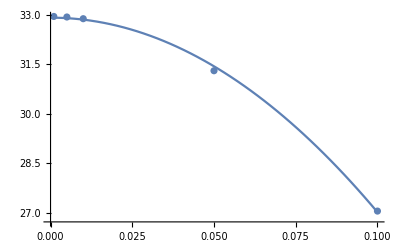

t-f: (finite momentum)   a_(d^*) = -0.0303873     r_(d^*) = -1179.43

>> The pole is at: {{p→-0.236229-0.0000473146 ⅈ},{p→0.+589.714 ⅈ},{p→0.236229-0.0000473146 ⅈ}}

--

{λ = ,2,   C0 = ,-142.376,   D0 = ,172.704}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

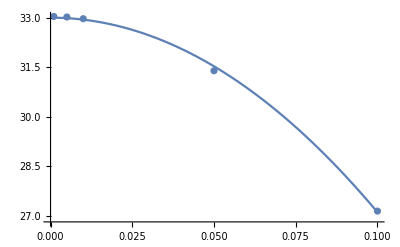

t-f: (finite momentum)   a_(d^*) = -0.0302933     r_(d^*) = -1181.58

>> The pole is at: {{p→-0.23638-0.0000472887 ⅈ},{p→0.+590.79 ⅈ},{p→0.23638-0.0000472887 ⅈ}}

--

{λ = ,3,   C0 = ,-295.959,   D0 = ,559.013}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

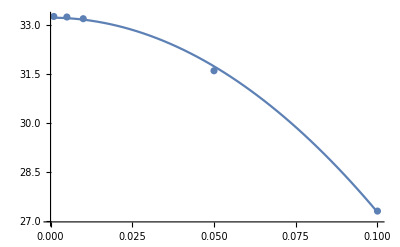

t-f: (finite momentum)   a_(d^*) = -0.030113     r_(d^*) = -1185.77

>> The pole is at: {{p→-0.236667-0.0000472364 ⅈ},{p→0.+592.884 ⅈ},{p→0.236667-0.0000472364 ⅈ}}

--

{λ = ,4,   C0 = ,-505.202,   D0 = ,1397.57}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

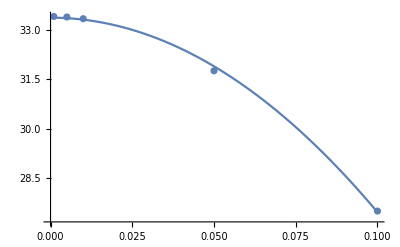

t-f: (finite momentum)   a_(d^*) = -0.0299501     r_(d^*) = -1189.62

>> The pole is at: {{p→-0.236926-0.0000471864 ⅈ},{p→0.+594.81 ⅈ},{p→0.236926-0.0000471864 ⅈ}}

--

{λ = ,6,   C0 = ,-1090.66,   D0 = ,6311.3}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

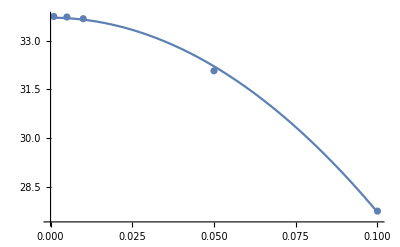

t-f: (finite momentum)   a_(d^*) = -0.0296682     r_(d^*) = -1196.43

>> The pole is at: {{p→-0.23737-0.0000470936 ⅈ},{p→0.+598.216 ⅈ},{p→0.23737-0.0000470936 ⅈ}}

--

{λ = ,10,   C0 = ,-2929.48,   D0 = ,89436.2}

{ * Fermion - Trimer star scattering * }

α3 is 0.00792452

General::munfl: Exp[-708.632] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.103] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.576] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.632] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.103] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.576] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.632] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.576] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.103] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.576] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

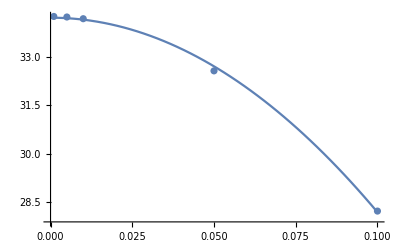

t-f: (finite momentum)   a_(d^*) = -0.0292198     r_(d^*) = -1207.69

>> The pole is at: {{p→-0.238066-0.0000469287 ⅈ},{p→0.+603.847 ⅈ},{p→0.238066-0.0000469287 ⅈ}}

--

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;

LEC0s={};
LED0s={};
αs={};
λs={};
a0s={};
affs={};

addLs={};
adds={};
addps={};
rddps={};
addstars={};
addstarsp={};
rddstarsp={};
afts={};
aftsp={};
aftsp={};
atfstarsp={};
rtfstarsp={};
(*Λl={1};*)


Do[{

Λ=Λl⟦j⟧;
λ=Transpose[LCD]⟦1⟧⟦j⟧;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;



AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

L=0;

(*Print parameters of the calculation*)
Print[Style[{"λ = ", λ,"   C0 = ", C0,"   D0 = ",D0},Blue,Bold,18]];





(* Microscopic calculation: *)
μ1=m/2;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
V0[r_]                   := C0  Exp[- λ r^2];
Vα0[Cc_,r_]       :=Cc  ⅇ^(-λ r^2);
W[r_,rp_,e_]  :=0;



(*Fit of the two body *)
If[Fit2b,
R=5;
C0=x/.FindRoot[Scatt1[x]^-1==aleph,{x,0.}];
Print["Fit try: C0: ",C0,"  a=",Scatt1[C0]];];



(*Calculate fermion fermion*)
If[CalculateFF,
Print[Style[{" * Fermion - Fermion scattering * "},Blue,Italic,14]];

nGrid     =100;
R             =10;
aff=SolveSecularNL0[R,nGrid,0.0,0]⟦1⟧;
(*Print[aamat//MatrixForm];*)

R=5;
Print[" > Finite Difference Method: a_ff = ", aff ];
Print[" > Variational Phase Method: aff = ",Scatt1[C0]];
aleph=aff^-1; (*Scatt1[C0]^-1;*)
α=1.5 5  aleph^2; (* useless if then you fit the correct dimer-dimer a*)
AppendTo[affs,    aff];
Print[""]];












If[CalculateDD,
(* Dimer - Dimer non-local*)
Print[Style[{" * Dimer - Dimer scattering * "},Blue,Italic,14]];
μ1=μ 2;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
nGrid=100;
Rmax=5;
ene=0.;
V0[r_]:=C0 ((2α)/(2α+λ))^(3/2) ⅇ^(-(2α λ)/(2α+λ)r^2);
W[r_,rp_,p_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+p^2)ⅇ^(-α(rp^2+r^2))-C0(32 √2 α^3)/(2α+λ)^(3/2)ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));


Print[" >> Fit α to have a_dd = 0.618 a_ff"];
(*************************)
(* I look for perfect α: *)
addwant=aleph^-1 * 0.618;
Print["  >  α_i           a_i         (a_wanted →  ", addwant,")"];
i=0;
αo=0.04;
αi=0.06;
xo=Block[{},{α=αo;tt=SolveSecularNL0[Rmax,nGrid,0.,0]⟦1⟧}]⟦1⟧;
xi=Block[{},{α=αi;tt=SolveSecularNL0[Rmax,nGrid,0.,0]⟦1⟧}]⟦1⟧;
While[(Abs[xi]>0.00001)||(i>10),
αt=αi-xi(αi-αo)/(xi-xo);
If[αt<0,αt=αi/2 ];
αo=αi;
αi=αt;
xo=xi;
xi=Block[{},{α=αi; tt=SolveSecularNL0[Rmax,nGrid,0.0,0]⟦1⟧}]⟦1⟧-addwant;
Print["  >  ",αi,"  ",xi+addwant];
i++;
];α=αi;
αl⟦j⟧=αi;
(*************************)



(*I do the real calculation of dd:*)
add=SolveSecularNL0[Rmax,nGrid,0.0,0]⟦1⟧;
Print[" >     α = ",α];
Print[" >  Finite Difference Method: a_dd = ", add ];
AppendTo[adds,    add];






(* Dimer - Dimer finite momentum *)
nGrid=1000;
Rmax=50;
Pp={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09, 0.1};
Pp={0.001,0.01,0.1};
Tp={};
Do[
Ti=SolveSecularNL0[Rmax,nGrid,Pp⟦i⟧,0]⟦1⟧;
AppendTo[Tp,Ti];
,{i,Range[Length[Pp]]}];
data=Transpose[{Pp,Tp}];
Ere=Fit[data,{1,p^2},p];
a0dd=-Coefficient[Ere,p,0]^-1;
r0dd= Coefficient[Ere,p,2]*2.;

Print[">>>>", Ere,"  ", a0dd,"  ",r0dd];

Show[ListPlot[data],Plot[Ere,{p,0,Pp⟦-1⟧}]];
Poledd= Solve[-a0dd^-1+0.5 r0dd p^2-ⅈ p ==0,p];
Print[" >  Finite momentum algorythm   a_dd = ",a0dd, "     r_dd = ", r0dd];
Print[" >> The pole is at: ", Poledd];
AppendTo[addps,    a0dd];
AppendTo[rddps,    r0dd];
Print[" "];];






If[CalculateDDstar,
(** Discrete scale invariant case **)
Print[Style[{" * Dimer - Dimer star scattering * "},Blue,Italic,14]];
μ1=2μ;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
nGrid=50;
Rmax=50;
ene=0.;
(*D0=0;*)

(* building the interaction is a little long*)
η2=3 C0((2 α)/(2α+λ))^(3/2);η3=D0((2 α)/(2α+λ))^3;η4=D0((2α)/(√((2α+λ)^2+2α λ)))^3;
ω2=(2 α λ)/(2α+λ);ω3=(4α λ)/(2α+λ);ω4=(4 α λ(α+λ))/(4 α^2+6 α λ+λ^2);
ξ1=8 α^(3/2)mh2^-1;ξ2=-8 α^(3/2)C0;ξ3=-16 α^(3/2)C0((2α)/(2α+λ))^(3/2);ξ4=-8 α^(3/2) D0 (α/(α+λ))^(3/2);ξ5=-8 α^(3/2)D0((2α(α+λ))/(2 α^2+α λ+λ^2))^(3/2);
a1=α;a2=α+λ;a3=(α(2α+3λ))/(2α+λ);a4=(2 α^2+4α λ+λ^2)/(2(α+λ));a5=(2 α^2+5α λ+λ^2)/(2α+λ);
b1=0;b2=2 λ;b3=0;b4=λ^2/(α+λ);b5=2λ;
c1=α;c2=α+λ;c3=α;c4=(2 α^2+4α λ+λ^2)/(2(α+λ));c5=α+λ;
V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2)+η4 ⅇ^(-ω4  r^2);
W[r_,rp_,p_]:=r rp 4 π(ξ1 ((4 a1^2 r^2-2 a1)+p^2)ⅇ^(-a1 r^2-c1 rp^2) -ξ2   (ⅇ^(b2 r rp-a2 r^2-c2 rp^2)-ⅇ^(-b2 r rp-a2 r^2-c2 rp^2))/(2 b2 r rp)   -ξ3 ⅇ^(-a3 r^2-c3 rp^2)-ξ4  (ⅇ^(b4 r rp-a4 r^2-c4 rp^2)-ⅇ^(-b4 r rp-a4 r^2-c4 rp^2))/(2 b4 r rp)-ξ5  (ⅇ^(b5 r rp-a5 r^2-c5 rp^2)-ⅇ^(-b5 r rp-a5 r^2-c5 rp^2))/(2 b5 r rp));



addstar=SolveSecularNL0[Rmax,nGrid,0.0,0]⟦1⟧;
AppendTo[addstars,    addstar];
Print["dd^*: λ = ", λ," α = ",α,"  C0 = ", C0, "  D0 = ",D0, " - FDM: a_(d^*) = ", addstar ];





(* Dimer^* - Dimer^* finite momentum *)
nGrid=500;
Rmax=50;
Pp={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09, 0.1};
Pp={0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009, 0.01};
Pp={0.001,0.01,0.1};
Tp={};
(*Print["       **  p         T            a"];*)
Do[
Ti=SolveSecularNL0[Rmax,nGrid,Pp⟦i⟧,0]⟦1⟧;
(*Print["       **  ",Pp⟦i⟧,"   " ,Ti,"   " ,-Ti^-1];*)
AppendTo[Tp,Ti];
,{i,Range[Length[Pp]]}];
data=Transpose[{Pp,Tp}];
Ere=Fit[data,{1,p^2},p];
a0dd=-Coefficient[Ere,p,0]^-1;
r0dd= Coefficient[Ere,p,2]*2.;

Show[ListPlot[data],Plot[Ere,{p,0,Pp⟦-1⟧}]]//Print;
Print["d^*d^*: (finite momentum)   a_(d^*) = ",a0dd, "     r_(d^*) = ", r0dd];
Print[">> The pole is at: ", Solve[-a0dd^-1+0.5 r0dd p^2-ⅈ p ==0,p]];

AppendTo[addstarsp,    a0dd];
AppendTo[rddstarsp,    r0dd];

Print[" "];
];







If[Calculate4H,
(** Trimer - Fermion case^4 H **)
Print[Style[{" * Fermion - Trimer star scattering * "},Blue,Italic,14]];
nGrid=50;
Rmax=50;
hbar=1;E3=-8.48;
R3=(-2m E3/hbar^2)^(-1/2);
α=R3;
Print["α3 is ", α];
Lrel=1;
ene=0.;
(*D0=0;*)

(* Trimer - Fermion case^4 H *)
μ1=3/4 m;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
η2=2 C0((3α)/(3α+λ))^(3/2);η3=8D0((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);
ω2=(3 α λ)/(3α+λ);ω3=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);
ξ1=27/8(3/2 α)^(3/2)mh2^-1;ξ2=-2 27 (3/2 α)^(3/2)C0(α/(4α+λ))^(3/2);ξ3=-27(3/2 α)^(3/2)D0(α/(4α+5 λ))^(3/2);

a1=15/16 α;a2=(3α(5α+8λ))/(4(4α+λ));a3=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));
b1=18/16 α;b2=(9α(α+λ))/(2(4α+λ));b3=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));
c1=15/16 α;c2=(3α(5α+2λ))/(4(4α+λ));c3=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));


V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2);
W[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+2/r^2-p^2) ⅈ SphericalBesselJ[1,ⅈ b1 r rp]-4 a1 b1 r rp (SphericalBesselJ[0,ⅈ b1 r rp]/Sqrt[3]
-SphericalBesselJ[2,ⅈ b1 r rp] 2/Sqrt[15]))+ξ2 ⅈ SphericalBesselJ[1,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)+ ξ3 ⅈ SphericalBesselJ[1,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];


(* Fermion - Trimer finite momentum *)
nGrid=300;
Rmax=8;
Pp={0.001,0.002,0.003,0.004,0.005,0.007,0.008,0.009,0.01,0.02};
Pp={0.001,0.005,0.01, 0.05, 0.1};
Tp={};
(*Print["       **  p         T            a"];*)

SetSharedVariable[Tpp];
Tpp=Pp;

ParallelDo[
Ti=ArcTan[SolveSecularNL1[Rmax,nGrid,Pp⟦i⟧,Lrel]⟦1⟧];

(*Print["       **  ",Pp⟦i⟧,"   " ,-Ti/Pp⟦i⟧^(2 Lrel+1)];*)
Tpp⟦i⟧=-Ti/Pp⟦i⟧^(2 Lrel+1);
,{i,Range[Length[Pp]]}
];


data=Transpose[{Pp,Tpp}];
Ere=Fit[data,{1,p^2},p];
a1dd=-Coefficient[Ere,p,0]^-1;
r1dd= Coefficient[Ere,p,2]*2.;

AppendTo[atfstarsp,    a1dd];
AppendTo[rtfstarsp,    r1dd];



(*ListPlot[data,GridLines->{{},{-2π,-1.5π,-π,-0.5π,0,0.5π,1π,1.5π,2π}}]//Print;*)
Show[ListPlot[data,GridLines->{{},{-2π,-1.5π,-π,-0.5π,0,0.5π,1π,1.5π,2π}}],Plot[Ere,{p,0,Pp⟦-1⟧}]]//Print;

Print["t-f: (finite momentum)   a_(d^*) = ",a1dd, "     r_(d^*) = ", r1dd];
Print[">> The pole is at: ", Solve[-a1dd^-1+0.5 r1dd p^2-ⅈ p^3 ==0,p]];


];




Print[" -- "];
Print[" "];
Print[" "];
},{j,1,Length[Λl]}];
```

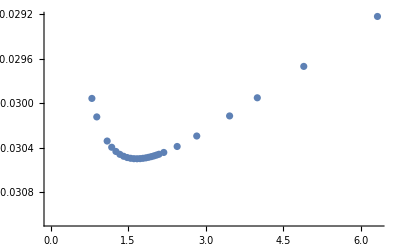

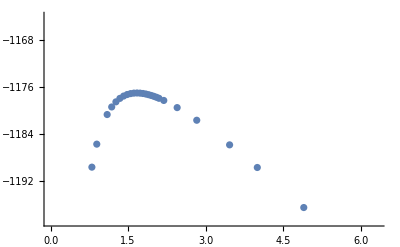

```mathematica
ListPlot[Transpose[{Λl,atfstarsp}]]
ListPlot[Transpose[{Λl,rtfstarsp}]]
```

```mathematica
Do[{ sol=Solve[-atfstarsp⟦i⟧^-1+0.5 rtfstarsp⟦i⟧ p^2-ⅈ p^3 ==0,p];
Print["Λ = ",Λl⟦i⟧,"    Re(p) = ",Abs[Re[p/.sol⟦1⟧]],"   Im(p) = ",Im[p/.sol⟦1⟧]];
Print["E = ", Re[mh2^-1(p/.sol⟦1⟧)^2], "     Γ = ",Im[ mh2^-1(p/.sol⟦1⟧)^2]*2];
},{i,1,Length[rtfstarsp]}];
```

Λ = 0.632456    Re(p) = 0.234124   Im(p) = -0.0000476004

E = 1.51546     Γ = 0.00123245

Λ = 0.8    Re(p) = 0.236909   Im(p) = -0.0000471818

E = 1.55173     Γ = 0.00123614

Λ = 0.894427    Re(p) = 0.236645   Im(p) = -0.0000472322

E = 1.54827     Γ = 0.00123609

Λ = 1.09545    Re(p) = 0.236301   Im(p) = -0.0000472961

E = 1.54378     Γ = 0.00123596

Λ = 1.18322    Re(p) = 0.236213   Im(p) = -0.0000473123

E = 1.54262     Γ = 0.00123592

Λ = 1.26491    Re(p) = 0.236153   Im(p) = -0.0000473232

E = 1.54184     Γ = 0.00123589

Λ = 1.34164    Re(p) = 0.236112   Im(p) = -0.0000473306

E = 1.54131     Γ = 0.00123587

Λ = 1.41421    Re(p) = 0.236085   Im(p) = -0.0000473357

E = 1.54095     Γ = 0.00123586

Λ = 1.48324    Re(p) = 0.236067   Im(p) = -0.000047339

E = 1.54072     Γ = 0.00123586

Λ = 1.54919    Re(p) = 0.236057   Im(p) = -0.0000473411

E = 1.54058     Γ = 0.00123586

Λ = 1.61245    Re(p) = 0.236051   Im(p) = -0.0000473423

E = 1.54052     Γ = 0.00123586

Λ = 1.67332    Re(p) = 0.23605   Im(p) = -0.0000473428

E = 1.5405     Γ = 0.00123587

Λ = 1.73205    Re(p) = 0.236053   Im(p) = -0.0000473426

E = 1.54053     Γ = 0.00123587

Λ = 1.78885    Re(p) = 0.236057   Im(p) = -0.0000473421

E = 1.54059     Γ = 0.00123588

Λ = 1.84391    Re(p) = 0.236064   Im(p) = -0.0000473411

E = 1.54068     Γ = 0.0012359

Λ = 1.89737    Re(p) = 0.236072   Im(p) = -0.0000473399

E = 1.54079     Γ = 0.00123591

Λ = 1.94936    Re(p) = 0.236082   Im(p) = -0.0000473385

E = 1.54092     Γ = 0.00123592

Λ = 2    Re(p) = 0.236093   Im(p) = -0.0000473368

E = 1.54106     Γ = 0.00123593

Λ = 2.04939    Re(p) = 0.236104   Im(p) = -0.000047335

E = 1.54121     Γ = 0.00123595

Λ = 2.09762    Re(p) = 0.236117   Im(p) = -0.000047333

E = 1.54137     Γ = 0.00123596

Λ = 2.19089    Re(p) = 0.236143   Im(p) = -0.0000473288

E = 1.54171     Γ = 0.00123599

Λ = 2.44949    Re(p) = 0.236229   Im(p) = -0.0000473146

E = 1.54284     Γ = 0.00123607

Λ = 2 √2    Re(p) = 0.23638   Im(p) = -0.0000472887

E = 1.54481     Γ = 0.00123618

Λ = 2 √3    Re(p) = 0.236667   Im(p) = -0.0000472364

E = 1.54857     Γ = 0.00123631

Λ = 4    Re(p) = 0.236926   Im(p) = -0.0000471864

E = 1.55195     Γ = 0.00123635

Λ = 2 √6    Re(p) = 0.23737   Im(p) = -0.0000470936

E = 1.55777     Γ = 0.00123623

Λ = 2 √10    Re(p) = 0.238066   Im(p) = -0.0000469287

E = 1.56693     Γ = 0.00123552